```mathematica
Quit
```

```mathematica
LaunchKernels[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
hasNan[data_] := Module[{}, (
Do[
If[AnyTrue[Head/@data[[Length[data]-i+1]], #===String&], Return[True, Module];Break[];]
, {i, 1, Length[data]}];
Return[False, Module];
)];
```

```mathematica
$K = 3;
```

```mathematica
SymTr[line_] := Module[{t, x}, (
Do[
t = First@line;
x[i] = line[[2+(i-1)(($N)^2-1);; 1+i(($N)^2-1)]];
, {i, 1, $K}];
{t, Table[x[i].x[j] - KroneckerDelta[i, j]/($K)Sum[x[k].x[k], {k, 1, $K}], {i, 1, $K}, {j, 1, $K}]}
)];
```

```mathematica
computeStats[data_] := Module[{rad, symTr, fns}, (
rad = radius/@data;
symTr = SymTr/@data;

fns = {Mean, StandardDeviation};

Join[{#[rad[[All, 2]]]&/@fns},
Flatten[#, 1]&@Table[#[symTr[[All, 2]][[i, j]]]&/@fns, {i, 1, $K-1}, {j, i, $K}]]
)];
```

```mathematica
If[!DirectoryQ["../../runs/Stats-New"], CreateDirectory["../../runs/Stats-New"]];
ParallelDo[Module[{$dirname, $files, $data, $stats, $out, statFile}, (
changeNK[$N, $K];
$dirname = "../../runs/Trials/N"<>ToString@$N<>"K"<>ToString@$K;
$files = FileBaseName/@FileNames[All, $dirname];
Do[(
$data = Import[$dirname<>"/"<>$files[[k]]<>".dat"];

If[hasNan[$data], Print["Detected nan, skipping"];Continue[]];

$stats = computeStats[$data];

$out = Join[{$files[[k]]}, Flatten@$stats];

statFile = OpenAppend["../../runs/Stats-New/N"<>ToString[$N]<>"K"<>ToString[$K]<>".dat"];
WriteString[statFile, StringRiffle[ToString/@$out, "    "]<>"\n"];
Close[statFile];
), {k, 1, Length[$files]}]
)], {$N, 5, 6}]
```

```mathematica
data = Import["../../runs/Trials/N9K9/16602768.dat"];
```

```mathematica
Export["../vals.dat", (radius/@data)[[All, 2]]]
```

../vals.dat

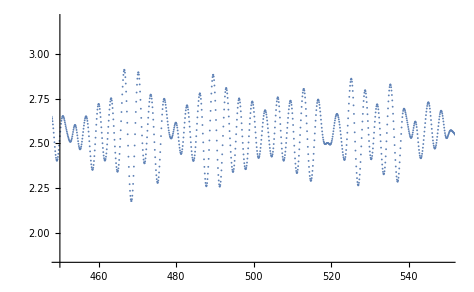

```mathematica
ListPlot[(radius/@data), PlotRange->{{450, 550}, Automatic}]
```

```mathematica
Export["../vals-2.dat",(SymTr/@data)[[All, 2]][[All, 1, 2]]]
```

../vals-2.dat

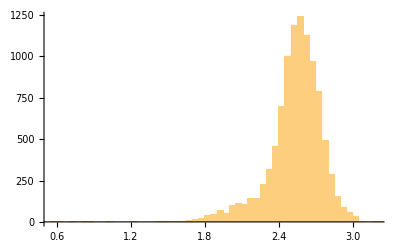

```mathematica
Histogram[(radius/@data)[[All, 2]], 100]
```

```mathematica
ShapiroWilkTest[(radius/@data)[[6000;;, 2]]]
```

0.0000197824

```mathematica
changeNK[9, 9];
```

```mathematica
cdata = cMat[data];
```

```mathematica
EigenvaluesContinuous[cdata_, $tSize_] := Module[{goodlist, eiglist}, (
goodlist = {{cdata[[1, 1]], Eigenvalues@cdata[[1, 2]]}};
eiglist = {Eigenvalues@cdata[[1, 2]]};
Module[{e, sortede, f}, Do[(
e = Eigenvalues[cdata[[t, 2]]];

sortede = Table[(
f = Quiet[Interpolation[eiglist[[All, m]]][Length[eiglist] + 1]];
First@Nearest[e, f]
), {m, 1, Length[e]}];

If[Length[eiglist] >= $tSize, 
eiglist = Append[eiglist[[2;;]], sortede], 
AppendTo[eiglist, sortede]
];

AppendTo[goodlist, {cdata[[t, 1]], sortede}];
), {t, 2, Length[cdata]}]];
goodlist
)];
```

```mathematica
ee = EigenvaluesContinuous[cdata, 50];
```

```mathematica
p  = Thread[{ee[[300;; 351, 1]],ee[[300;;351, 2, 1]]}]
```

{{29.9,0.773639},{30,0.777672},{30.1,0.779602},{30.2,0.779717},{30.3,0.778341},{30.4,0.775795},{30.5,0.772379},{30.6,0.768351},{30.7,0.763929},{30.8,0.759304},{30.9,0.754664},{31,0.750224},{31.1,0.746245},{31.2,0.743031},{31.3,0.740879},{31.4,0.740014},{31.5,0.7405},{31.6,0.742206},{31.7,0.744816},{31.8,0.747888},{31.9,0.750915},{32,0.75338},{32.1,0.754784},{32.2,0.754659},{32.3,0.752588},{32.4,0.748207},{32.5,0.741219},{32.6,0.731407},{32.7,0.718644},{32.8,0.702899},{32.9,0.684238},{33,0.66283},{33.1,0.63894},{33.2,0.612941},{33.3,0.585351},{33.4,0.556921},{33.5,0.528877},{33.6,0.503408},{33.7,0.484112},{33.8,0.474015},{33.9,0.471564},{34,0.472766},{34.1,0.474909},{34.2,0.476663},{34.3,0.477369},{34.4,0.476655},{34.5,0.474281},{34.6,0.470097},{34.7,0.464039},{34.8,0.45616},{34.9,0.446682},{35,0.436215}}

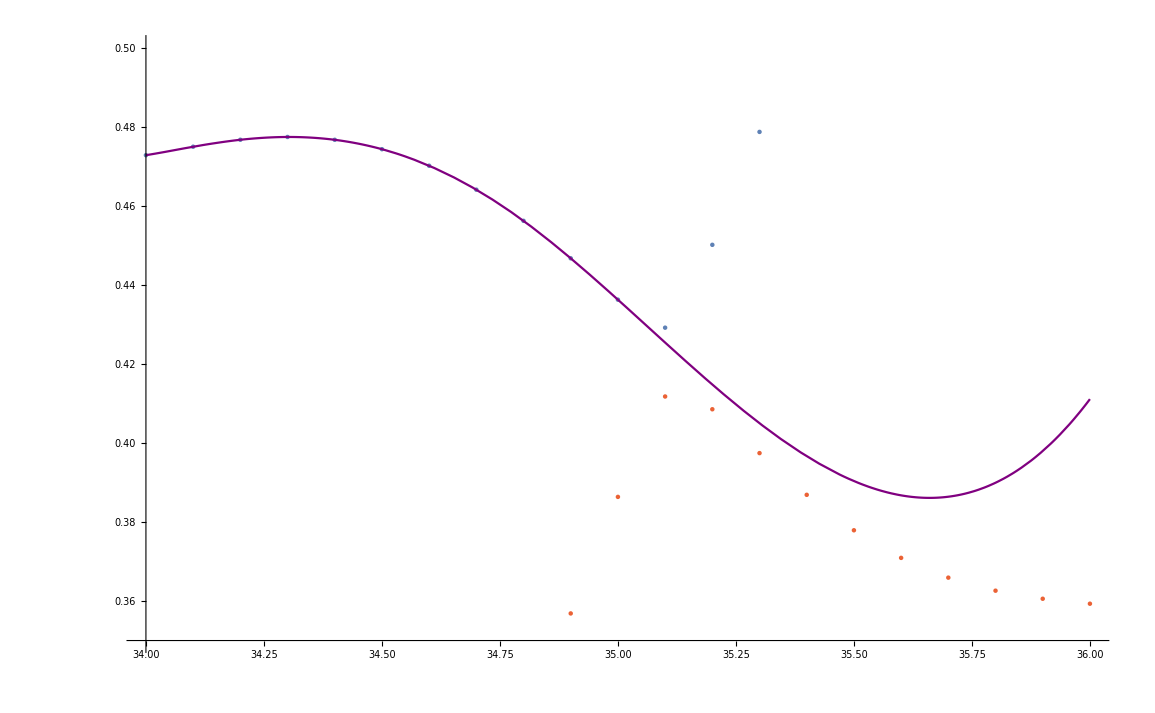

```mathematica
Show[ListPlot[Thread[Table[{#[[1]], y}, {y, #[[2]]}]&/@ee], PlotRange->{{34, 36}, {0.35, 0.5}}], Plot[Interpolation[p][t], {t, 34, 36},PlotStyle->Purple]]
```

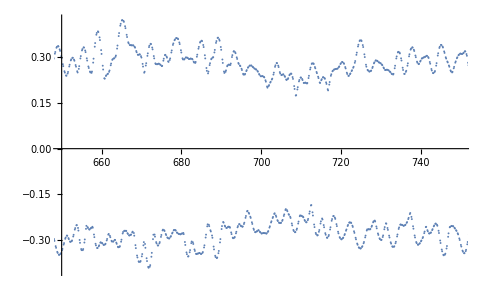

```mathematica
ListPlot[Thread[{ee[[All, 1]],ee[[All, 2, 5]]}], PlotRange->{{650, 750}, Automatic}]
```

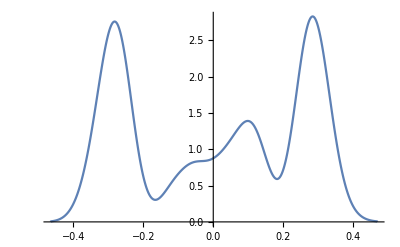

```mathematica
SmoothHistogram[ee[[All, 2, 5]]]
```